# NewMazePaclet

XXXX | XXXX
XXXX | XXXX
XXXX | XXXX

XXXX.

Create a grid graph.

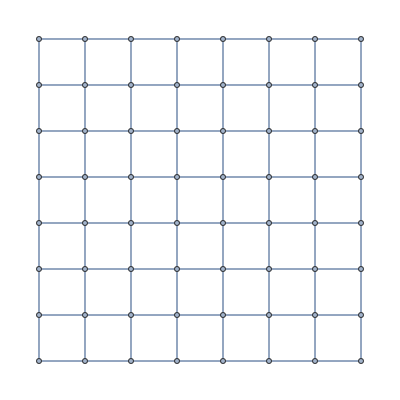

```mathematica
gridGraph=GridGraph[{8,8}]
```

Create a triangular grid graph.

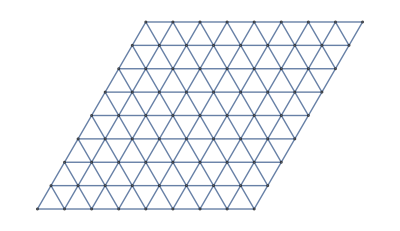

```mathematica
triangularGridGraph=TriangularGridGraph[{8,8}]
```

Create a hexagonal graph.

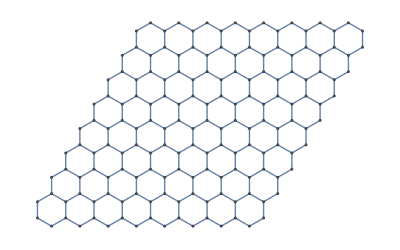

```mathematica
hexagonalGridGraph=HexagonalGridGraph[{8,8}]
```

Make a maze for each type of grid.

square grid:

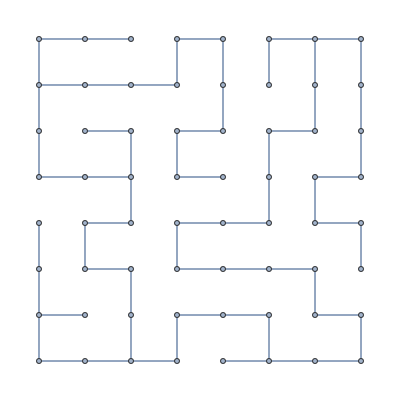

```mathematica
gridMaze=MakeMaze[gridGraph]
```

Triangular grid:

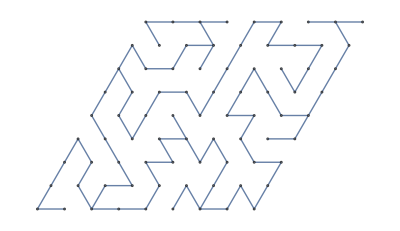

```mathematica
triangularMaze=MakeMaze[triangularGridGraph]
```

Hexagonal grid:

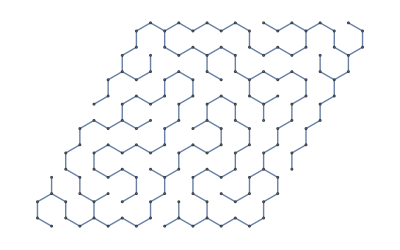

```mathematica
hexagonalMaze=MakeMaze[hexagonalGridGraph]
```

The main function of the paclet is SolveMaze. Solve the mazes.

Square maze solution:

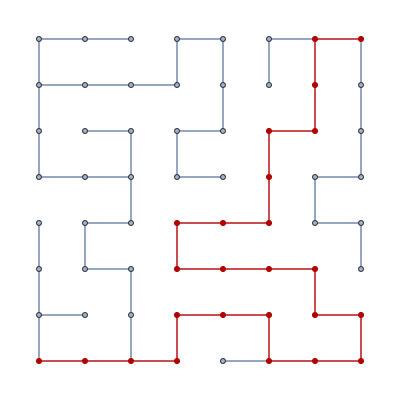

```mathematica
squareMazeSolution=SolveMaze[gridMaze]
```

Triangular maze solution:

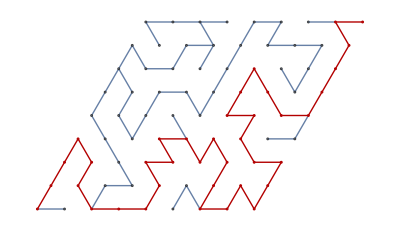

```mathematica
triangularMazeSolution=SolveMaze[triangularMaze]
```

Hexagonal maze solution:

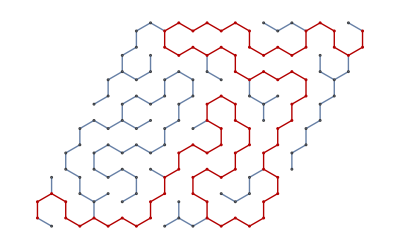

```mathematica
hexagonalMazeSolution=SolveMaze[hexagonalMaze]
```

There's also a function that will generate an equilateral triangle.

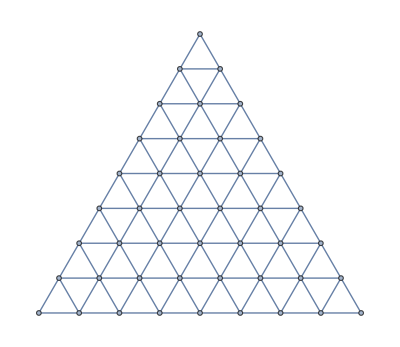

```mathematica
equilateralTriangleGraph=EquilateralTriangleGraph[8]
```

Make a maze:

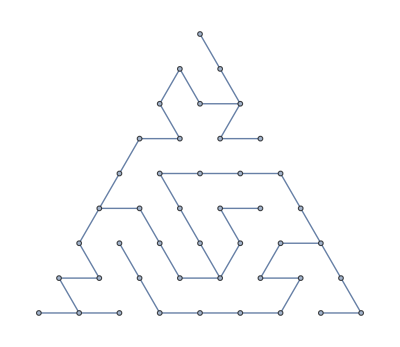

```mathematica
equilateralTriangleMaze=MakeMaze[equilateralTriangleGraph]
```

Solve the maze:

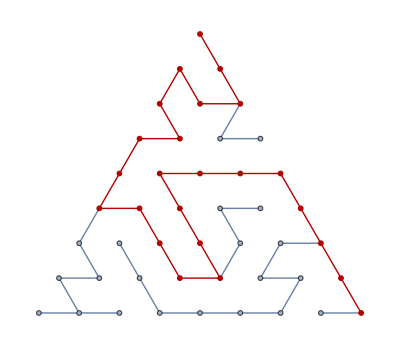

```mathematica
equilateralTriangleMaze=SolveMaze[equilateralTriangleMaze]
```

The problem with this function is it doesn't regularly tile the plane. You can't specify a different width and height, which you can do with TriangularGridGraph.

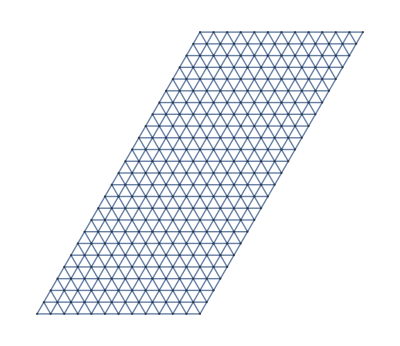

```mathematica
TriangularGridGraph[{12,24}]
```

You can only generate a 12 equilateral triangle or a 24 equilateral triangle.

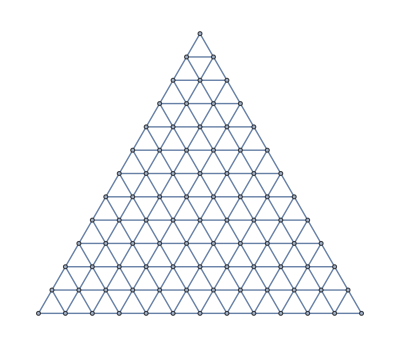

```mathematica
EquilateralTriangleGraph[12]
```

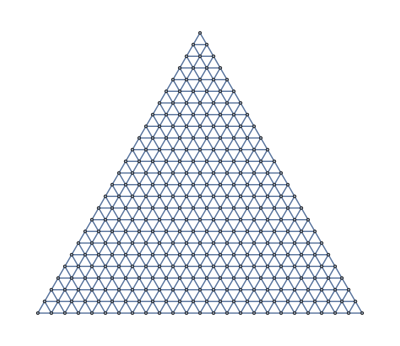

```mathematica
EquilateralTriangleGraph[24]
```

You can represent a maze with a tree:

```mathematica
GraphTree[triangularMaze]
```

-Graphics-

You can contract the edges of the tree of the graph.

```mathematica
VertexDelete[triangularMaze,]
```

```mathematica
VertexDegree[triangularMaze]
```

{2,1,3,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,1,2,2,2,2,1,2,2,2,2,3,2,2,2,2,2,2,2,2,2,3,2,2,1,2,2,1,2,2,2,1,2,3,2,2,2,2,2,2,2,3,1,2,2,1,3,1}

```mathematica
Position[VertexDegree[triangularMaze],2]
```

{{1},{4},{5},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{33},{34},{36},{37},{38},{39},{41},{42},{43},{44},{46},{47},{48},{49},{50},{51},{52},{53},{54},{56},{57},{59},{60},{62},{63},{64},{66},{68},{69},{70},{71},{72},{73},{74},{77},{78}}

```mathematica
Flatten[Position[VertexDegree[triangularMaze],2]]
```

{1,4,5,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,33,34,36,37,38,39,41,42,43,44,46,47,48,49,50,51,52,53,54,56,57,59,60,62,63,64,66,68,69,70,71,72,73,74,77,78}

```mathematica
Extract[VertexList[triangularMaze],Position[VertexDegree[triangularMaze],2]]
```

{1,12,20,50,60,2,5,9,16,25,36,46,56,66,4,8,13,21,31,41,51,61,71,7,11,17,26,47,57,77,10,15,22,42,52,62,72,14,19,27,38,48,58,68,78,86,24,33,53,63,82,89,23,39,59,69,79,87,93,28,35,65,75}

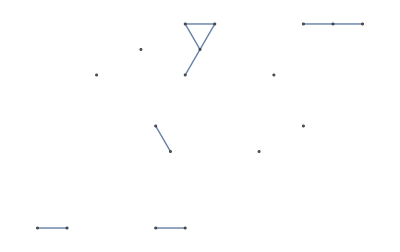

```mathematica
VertexDelete[triangularGridGraph,Extract[VertexList[triangularMaze],Position[VertexDegree[triangularMaze],2]]]
```

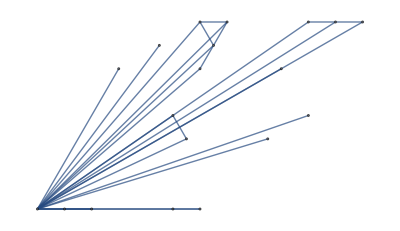

```mathematica
VertexContract[triangularGridGraph,Extract[VertexList[triangularMaze],Position[VertexDegree[triangularMaze],2]]]
```

```mathematica
GraphTree[VertexContract[triangularGridGraph,Extract[VertexList[triangularMaze],Position[VertexDegree[triangularMaze],2]]]]
```

GraphTree[-Graphics-]

```mathematica
tree=RandomTree[7]
```

-Graphics-

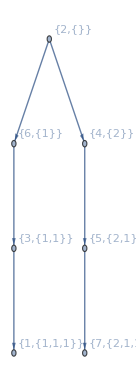

```mathematica
graph=TreeGraph[tree,VertexLabels->"Name"]
```

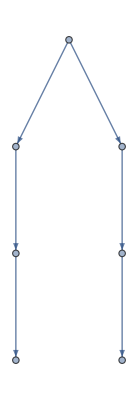

```mathematica
CanonicalGraph[graph]
```

```mathematica
graph=Graph[CanonicalGraph[graph],VertexLabels->"Name"]
```

-Graphics-

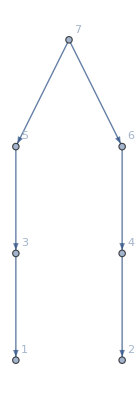
VertexContract[-Graphics-,3]

```mathematica
VertexContract[graph,3]
```

```mathematica
VertexContract[graph,{3}]
```

-Graphics-

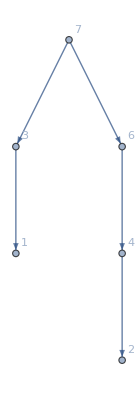

```mathematica
VertexContract[graph,{3,5}]
```

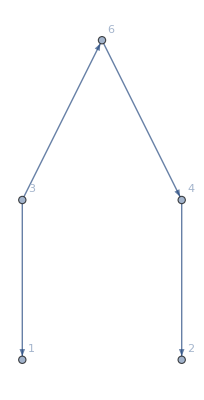

```mathematica
VertexContract[graph,{3,5,7}]
```

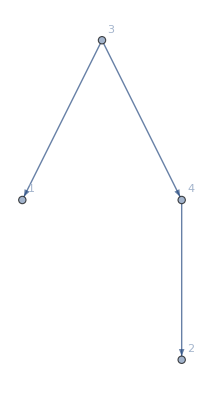

```mathematica
VertexContract[graph,{3,5,7,6}]
```

```mathematica
VertexContract[graph,{3,5}]
```

-Graphics-

```mathematica
VertexContract[VertexContract[graph,{3,5}],{6,4}]
```

-Graphics-

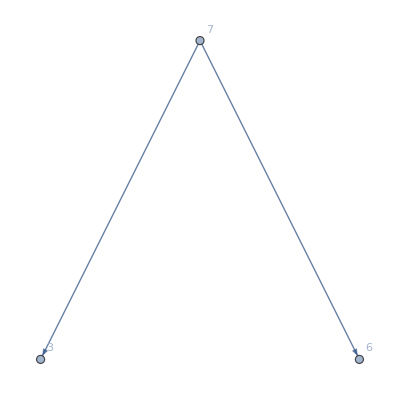

```mathematica
VertexContract[VertexContract[graph,{3,5,1}],{6,4,2}]
```

```mathematica
Vertex
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

PeterBurbery/NewMazePaclet

PeterBurbery`NewMazePaclet`

PeterBurbery/NewMazePaclet/tutorial/NewMazePaclet

### Keywords